```mathematica
Needs["NDSolve`FEM`"]
```

# Circular integration test with better boundaries

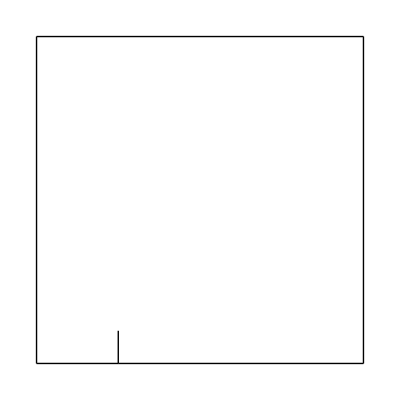

```mathematica
boundary = ToBoundaryMesh[
"Coordinates"->{
{0,0},
{0.25,0},
{0.25,0.1},
{1,0},
{1,1},
{0,1}
},
"BoundaryElements"->{
LineElement[{
{1,2},
{2,3},
{2,4},
{4,5},
{5,6},
{6,1}},
{2,2,2,2,2,2}
]
}
];
reg = ToElementMesh[boundary,
"MeshQualityGoal"->0.7, 
"MaxCellMeasure"->{"Area"->0.01},
MeshRefinementFunction->Function[{vertices,area},(area ≥0.00001Norm[{0.25,0.1}-Mean[vertices]])]
];
boundary["Wireframe"]
```

```mathematica
sol=NDSolveValue[
{
Laplacian[u[x,y],{x,y}]+1==0,
{DirichletCondition[u[x,y]==0,x≤0||x≥1||y≤0||y≥0],
DirichletCondition[u[x,y]==0,x==0.25&&y≥0&&y≤0.1]}
},
u,
{x,y}∈reg,
AccuracyGoal->25,PrecisionGoal->25];
```

```mathematica
Show[
ContourPlot[sol[x,y],{x,y}∈reg],
Graphics[{
Red, Circle[{0.25,0.1},0.1], 
White, Point[{0.25,0.1}]}]
]
```

-Graphics-

#### Now we will integrate in circle

```mathematica
DiskIntegr=NIntegrate[sol[x,y],{x,y}∈Disk[{0.25,0.1},0.1],AccuracyGoal->20,PrecisionGoal->15, MaxRecursion->45]//Quiet
RealDigits[DiskIntegr]
```

0.000461138

{{4,6,1,1,3,8,2,3,4,4,4,6,5,3,6,3},-3}

Value evaluated from FreeFem++ is 0.000461324 relative difference is 0.04%.

```mathematica
(0.000461324 - 0.0004611382344465363)/0.000461324 * 100
```

0.0402679

#### Whole region

```mathematica
wholeRigIntegr=NIntegrate[sol[x,y],{x,y}∈reg,AccuracyGoal->20,PrecisionGoal->7,MaxRecursion->45]
RealDigits[wholeRigIntegr]
```

0.034202

{{3,4,2,0,2,0,2,3,6,0,8,5,7,1,0,2},-1}

Value evaluated from FreeFem++ is 0.034202 relative difference is 0.00005%!!!

```mathematica
0.0000000202360857102/0.03420202360857102*100
```

0.0000591663

#### Max Value of function

```mathematica
maxval=NMaxValue[sol[x,y],{x,y}∈reg]//Quiet;
RealDigits[maxval]
Print[maxval]
```

{{7,2,5,7,9,2,1,8,3,4,6,0,3,5,5,1},-1}

0.0725792

# Test With exact implementation like in FreeFem++

```mathematica
BaseVector[nf_Integer, zf_Complex]:=If[Mod[nf,2]==0,-Im[zf^(nf/2.)],Re[zf^(nf/2.)]]
```

### predefined integral

```mathematica
R = 0.01(*same radius is in freefem*);
exponant = 2(*value from FreeFem*);
tipangle = Pi/2;
x0 = 0.25;
y0 = 0.1;

a[order_Integer]:=
NIntegrate[
sol[x,y] 
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) 
],
{x,y}∈Disk[{x0,y0},R],
AccuracyGoal->20, 
PrecisionGoal->7,
MaxRecursion->50,
WorkingPrecision->16]/
NIntegrate[
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) ]^2,
{x,y}∈Disk[{x0,y0},R],
AccuracyGoal->20, 
PrecisionGoal->7,
MaxRecursion->50,
WorkingPrecision->16]
```

### And final value check!

```mathematica
a[1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.102110587511622

```mathematica
a[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8871472970103464717692747871728417304598631667630513929703929134×10^-10 and 2.12036174630272643855848654755380635564827673908302454983934608102×10^-16 for the integral and error estimates.

0.0454658719778866

```mathematica
a[3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.88361627959472893279644492349467208608360714258887268063907147418×10^-12 and 1.60094472597134021258894435477084883424247481129329272768335405106×10^-17 for the integral and error estimates.

0.123287949871927

#### Now lets compare these series params with what are from FreeFem

```mathematica
(0.102110587511622424669761935715423-0.101866)/0.101866*100
```

0.240107

0.2% of difference for a1

```mathematica
(0.0454658719778 - 0.0454618)/0.0454618*100
```

0.00895692

0.008% of difference for a2

```mathematica
(-0.1232879498719 + 0.13087)/0.1232879498719 *100
```

6.14987

6 % of difference for a3

# From Simpler Formula without BaseVector

### TODO later.. ask Piotr Szymczak about this problem..